```mathematica
"Project Thesis Superconductors"
"Numerical Fermi-Dirac Distribution and Entropy Calculation"
```

Project Thesis Superconductors

Numerical Fermi-Dirac Distribution and Entropy Calculation

```mathematica
(* Clear all variables as follows: *)
(* ClearAll["Global`*"] *)

(* Load Numerical Calculus Package *)
<<NumericalCalculus`
(* <<NonlinearRegression` *)

(* Constants *)
	kB=1.3806482*10^(-23); (* Boltzmann Constant *)
	Tc=2.05;
	AlphaBCS=1.764;
	gamma=1*kB;

(* Differentiation Parameters *)
	n=0.0001;(*start value*)
	m=1.01;(*endvalue*)
	in=0.0005;(*incremental value*)

(* Experimental Data *)
	jGap=Import["Documents/coding/sl_code/data/johnson_band_gap_data.csv","CSV"];
	mGap  = Import["Documents/coding/sl_code/data/muehlschlegel_data_Bandgap.csv","CSV"];
	mEnt= Import["Documents/coding/sl_code/data/muehlschlegel_data_Entropy.csv","CSV"];
	mHCap= Import["Documents/coding/sl_code/data/muehlschlegel_data_Heat_Capacity.csv","CSV"];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
a | -4.06181 | 1.20045 | -3.38358 | 0.00190474
b | -4.07055 | 1.19382 | -3.40969 | 0.00177613
c | 11.4969 | 3.97224 | 2.89431 | 0.00678997
d | 11.6771 | 3.85625 | 3.02811 | 0.00483434
e | -16.5437 | 8.11781 | -2.03795 | 0.049892
f | -17.9131 | 7.3349 | -2.44217 | 0.0203048
g | 7.92016 | 11.8554 | 0.668064 | 0.508883
h | 12.3709 | 9.4388 | 1.31064 | 0.199308
i | 2.14757 | 9.3539 | 0.229591 | 0.819871
j | -3.16789 | 6.4985 | -0.48748 | 0.629241
k | -1.95907 | 2.81103 | -0.696923 | 0.490883
l | 0.10439 | 1.70306 | 0.0612954 | 0.951505

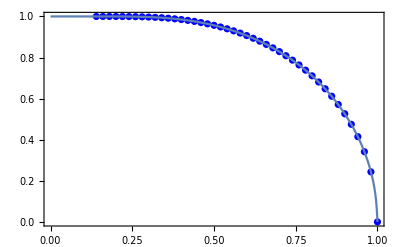

```mathematica
(* Demonstration of the band gap fit *)
(* reset all variables before running this field *)
deltaFit = NonlinearModelFit[mGap,(1+a*T+c*T^2+e*T^3+g*T^4+i*T^5+k*T^6)/(1+b*T+d*T^2+f*T^3+h*T^4+j*T^5+l*T^6),{a,b,c,d,e,f,g,h,i,j,k,l},T];
deltaFit["ParameterTable"]

(* Demonstration Band Gap Plot in Comparison with Muelschlegel Data *)	
Show[ListPlot[mGap, PlotStyle->Blue], Plot[deltaFit[T],{T,0,1}],Frame->True]
```

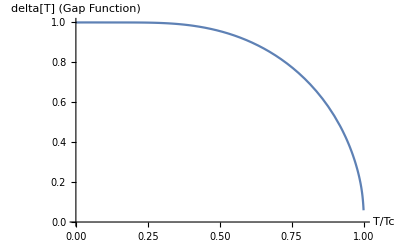

```mathematica
(* Parameters Extracted from Band Gap Fit *)
	a=-4.06181;
	b=-4.07055;
	c=11.4969;
	d=11.6771;
	e=-16.5437;
	f=-17.9131;
	g=7.92016;
	h=12.3709;
	i=2.14757;
	j=-3.16789;
	k=-1.95907;
	l=0.10439;

	delta= (1+a*t+c*t^2+e*t^3+g*t^4+i*t^5+k*t^6)/(1+b*t+d*t^2+f*t^3+h*t^4+j*t^5+l*t^6);

(* Band Gap Plot *)
	Plot[delta,{t,0,1.}, AxesLabel->{"T/Tc", "delta[T] (Gap Function)"}]
```

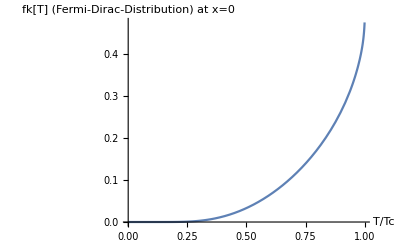

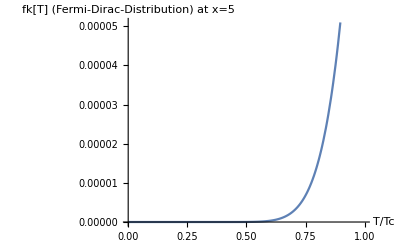

```mathematica
(* Fermi-Dirac-Distribution *)
	(* Units: None *)
	fx:=(Exp[AlphaBCS/t*(x^2+delta^2)^(1/2)]+1)^(-1);

(* Fermi-Dirac-Distribution Plot *)
x=0;
Plot[fx,{t,0,1.}, AxesLabel->{"T/Tc", "fk[T] (Fermi-Dirac-Distribution) at x=0"}]

(* Fermi-Dirac-Distribution Plot *)
x=5;
Plot[fx,{t,0,1.}, AxesLabel->{"T/Tc", "fk[T] (Fermi-Dirac-Distribution) at x=5"}]
```

```mathematica
(* Electronic Entropy *)
	tmpFunc=Table[-6*AlphaBCS/Pi^2*NIntegrate[(fx*Log[fx]+(1-fx)*Log[1-fx]),{x,0,1000}],{t,n,m,in}];
	q:=Round[(t-n+in)/in];
	Ses=N[Table[{t,tmpFunc[[q]]},{t,n,m,in}]];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.152697}. NIntegrate obtained -6.40604×10^-16 and 8.64564×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.219836}. NIntegrate obtained -9.36682×10^-16 and 8.40306×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.260149}. NIntegrate obtained -1.35895×10^-15 and 3.25755×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

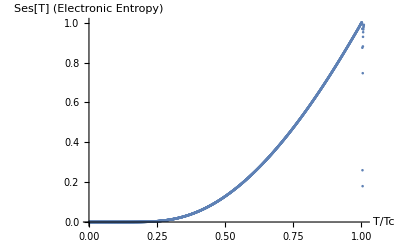

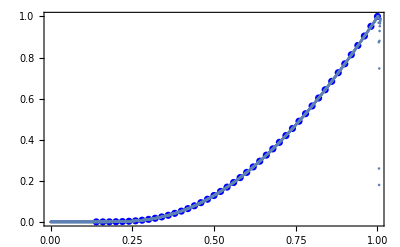

```mathematica
(* Electronic Entropy Plot *)
	ListPlot[Ses, AxesLabel->{"T/Tc", "Ses[T] (Electronic Entropy)"}]
	Show[ListPlot[mEnt, PlotStyle->Blue], ListPlot[Ses, AxesLabel->{"T/Tc", "Ses[T] (Electronic Entropy)"}],Frame->True]
```